# NG^21 P_10.Автоматическое дифференцирование. Свёртка

Бельской Екатерины,
2 курс, 5 группа

```mathematica
SetDirectory@NotebookDirectory[];
Begin["NG21P10`"];
Get["NG21P10Problem.mx","NG21P10"];
End[];
```

ClearAll[symb_1,symb_2,…] clears all values, definitions, attributes, messages, and defaults associated with symbols. 
ClearAll[form,form,…] clears all symbols whose names textually match any of the form_i.

## 1. Подвижные числа

```mathematica
MN=NG21P10`kmMN;
```

```mathematica
MN[2,1]+MN[3,1]
```

5+2𝔢

```mathematica
ex=D[Sin[x]+Log[x]+x^2/6,x]
```

1/x+x/3+Cos[x]

```mathematica
ex/.x->1
```

4/3+Cos[1]

```mathematica
ex/.x->MN[5,6]
```

```mathematica
MN[5,6]
```

5+6𝔢

```mathematica
MN[1,3]
```

1+3𝔢

```mathematica
MN[MN[5,3],MN[2,1]]
```

5+5𝔢

```mathematica
5^MN[2,3]
```

25+75 Log[5]𝔢

## 2. Реализация подвижных чисел

kmMN[x1,y1] kmMN[x2,y2]=(x1+y1*𝔢 )(x2+y2*𝔢)=x1*x2 + x1*y2*𝔢+ x2*y1*𝔢 = kmMN[x1*x2,x1*y2+x2*y1]
kmMN[x1,y1]/kmMN[x2,y2]=(x1+y1*𝔢 )/(x2+y2*𝔢)=((x1+y1*𝔢 )(x2-y2*𝔢))/((x2+y2*𝔢)(x2-y2*𝔢))=(x1*x2 - x1*y2*𝔢+ x2*y1*𝔢)/x2^2 = x1/x2  + (y1*𝔢)/x2 -  (x1*y2*𝔢)/x2^2 = kmMN[ x1/x2 , y1/x2 -  (x1*y2)/x2^2]
kmMN[ kmMN[x1,y1],kmMN[x2,y2]]=kmMN[x1,y1]+ kmMN[x2,y2]𝔢=x1+y1*𝔢 + (x2+y2*𝔢)*𝔢 = x1 +y1*𝔢+x2*𝔢= kmMN[x1,y1+x2]
a^kmMN[x,y]= a^x+ Ln[a]a^x y*𝔢 = kmMN[ a^x, Ln[a]a^x y]

```mathematica
ClearAll[kmMN];
kmMN/:MakeBoxes[kmMN[0|0.,y_?Positive],form_]:=
	RowBox[{MakeBoxes[y,form],"𝔢"}];
kmMN/:MakeBoxes[kmMN[0|0.,y_?Negative],form_]:=With[{my=-y},
	RowBox[{"-",MakeBoxes[my,form],"𝔢"}]];
kmMN/:MakeBoxes[kmMN[x_,y_?Positive],form_]:=
	RowBox[{MakeBoxes[x,form],"+",MakeBoxes[y,form],"𝔢"}];
kmMN/:MakeBoxes[kmMN[x_,y_?Negative],form_]:= With[{my=-y},
	RowBox[{MakeBoxes[x,form],"-",MakeBoxes[my,form],"𝔢"}]];
𝔢=kmMN[0,1];
kmMN[x_,0|0.]:=x;
kmMN/:a_+kmMN[x_,y_]:=kmMN[a+x,y];
kmMN/:a_ kmMN[x_,y_]:=kmMN[a x, a y];
kmMN[kmMN[x1_,y1_],kmMN[x2_,y2_]]:=kmMN[x1,x2+y1];
kmMN/:kmMN[x1_,y1_]+kmMN[x2_,y2_]:=kmMN[x1+x2,y1+y2];
kmMN/:kmMN[x1_,y1_]kmMN[x2_,y2_]:=kmMN[x1 x2,x1 y2+x2 y1 ];
kmMN/:kmMN[x1_,y1_]/kmMN[x2_,y2_]:=kmMN[x1/x2,(-y2*x1)/x2^2+y1/x2];
kmMN/:kmMN[x_,y_]^a_/;FreeQ[a,x]:=kmMN[x^a,a x^(a-1) y];
kmMN/:a_^kmMN[x_,y_]/;FreeQ[a,x]:=kmMN[a^x,a^x y Log[a]];
kmMN/:(F_/;MemberQ[Attributes@F,NumericFunction])[kmMN[x_,y_]]:=kmMN[F[x],y F'[x]];
```

```mathematica
kmMN[kmMN[1,5],kmMN[2,3]]
```

1+7𝔢

```mathematica
MN[MN[1,5],MN[2,3]]
```

1+7𝔢

```mathematica
MN[1,5]
```

1/2+7/4 𝔢

```mathematica
2*kmMN[1,5]
```

2+10𝔢

## 3. Вычисление производных

```mathematica
F3=NG21P10`kmF3;
```

```mathematica
F3[20]
```

1.28741

```mathematica
F3
```

Piecewise[{{1-#1, #1<1}, {#1-1, #1<2}, {1, #1<3}, {1/5 (28 #1^2-201 #1+361), #1<4}, {Sin[π (#1-3)^1.5]+1, True}}]&

False

```mathematica
π (kmMN[5,5]-3)^1.5
```

π (2.82843+10.6066𝔢)

```mathematica
Sin[π*(kmMN[5,5]-3)^1.5]+1
```

1.51329-28.5972𝔢

```mathematica
F3[5]
```

1.51329

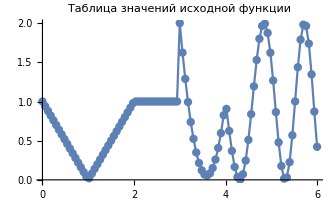

```mathematica
ListLinePlot[{#,F3@#}&/@Subdivide[6,100],PlotLabel->"Таблица значений исходной функции",AspectRatio->Automatic,Mesh->Full]
```

```mathematica
table={#,F3[#]}&/@Subdivide[6,100];
```

```mathematica
table1=MapThread[{#1,#2}&,{Most[table⟦;;,1⟧],ListConvolve[{1,-1},table⟦;;,2⟧]/(6/100)}];
```

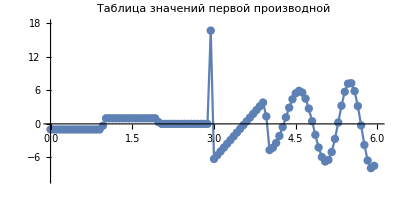

```mathematica
ListLinePlot[table1,PlotLabel->"Таблица значений первой производной",PlotRange->{{0,6},{-10,18}},AspectRatio->1/2,Mesh->Full]
```

```mathematica
Dt
```

```mathematica
temp={#,F3'[#]}&/@Subdivide[6,100];
```

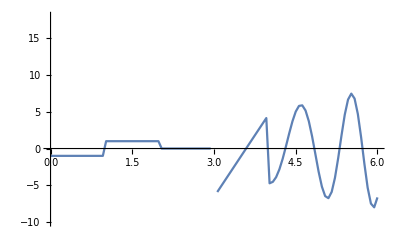

```mathematica
ListLinePlot[temp,PlotRange->{{0,6},{-10,18}}]
```

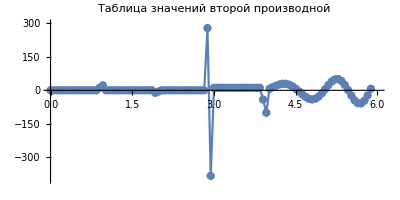

```mathematica
ListLinePlot[MapThread[{#1,#2}&,{Most[Most[table⟦;;,1⟧]],ListConvolve[{1,-1},table1⟦;;,2⟧]/(6/100)}],PlotLabel->"Таблица значений второй производной",PlotRange->{{0,6},{-400,300}},AspectRatio->1/2,Mesh->Full]
```

```mathematica
temp2={#,F3''[#]}&/@Subdivide[6,100];
```

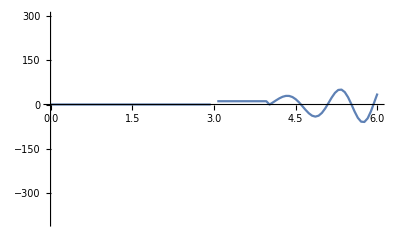

```mathematica
ListLinePlot[temp2,PlotRange->{{0,6},{-400,300}}]
```

Примеры показывают, что вычисление производных, используя операцию свертки помогает найти значение производных во всех точках

## 4. Сглаживание

```mathematica
F4=NG21P10`kmF4;
```

```mathematica
F4
```

2 Sin[√#1]+Sin[3 #1^0.7]&

```mathematica
ar=Subdivide[10,100];
```

```mathematica
tb={#,F4@#}&/@ar;
```

```mathematica
n=RandomVariate[NormalDistribution[0,0.2],Length@tb]
```

{-0.0318778,-0.254066,-0.14657,-0.169276,0.249398,0.047604,0.144999,0.44101,-0.382683,0.128241,0.0351061,-0.261108,-0.216521,-0.301776,-0.535902,-0.160157,-0.316602,0.169006,0.00213881,-0.0843796,-0.157123,0.0522692,-0.15581,-0.449579,-0.146859,-0.00191893,0.0776615,0.207992,0.228294,-0.332522,0.229517,0.35451,-0.133751,-0.0680192,0.396056,-0.0562756,-0.0280984,0.0948799,-0.00968488,0.127721,0.140486,-0.269242,-0.0882472,0.0637465,0.287424,0.233621,-0.333194,-0.270777,-0.467394,0.194271,-0.149839,-0.0970378,-0.0531203,-0.206904,-0.204073,-0.213946,-0.405287,0.0297829,-0.238331,-0.181339,-0.211542,0.388039,-0.068263,-0.348998,0.173938,-0.0977623,0.104183,-0.180752,0.0769415,-0.0991853,-0.204857,0.323266,-0.0937421,0.221168,0.0338855,0.233759,0.134215,0.00358729,0.282818,0.216285,-0.0539617,-0.0523955,-0.15424,-0.297579,-0.21385,0.00755328,-0.164302,-0.060368,-0.564755,-0.0327508,0.0550917,-0.384361,0.00716239,0.180193,-0.0309485,-0.0844556,-0.035316,-0.101792,0.09745,0.192551,0.141829}

```mathematica
Length[tb]
```

101

```mathematica
tn=MapThread[{#1,#2}&,{tb⟦;;,1⟧,tb⟦;;,2⟧+n}];
```

```mathematica
GaussianMatrix[{{5}}]
```

{0.0216149,0.0439554,0.0778778,0.118718,0.153857,0.167953,0.153857,0.118718,0.0778778,0.0439554,0.0216149}

```mathematica
ListConvolve[GaussianMatrix[{{5}}],t1⟦;;,2⟧]
Length@%
```

{1.91013,1.97498,1.96062,1.89586,1.79643,1.67514,1.54287,1.40887,1.28086,1.16519,1.06683,0.989506,0.935754,0.907012,0.903731,0.925474,0.971037,1.03856,1.12563,1.22943,1.34681,1.47441,1.60876,1.74637,1.88381,2.01779,2.14521,2.26323,2.36931,2.46124,2.53718,2.59566,2.63561,2.65632,2.65749,2.63916,2.60175,2.54598,2.47287,2.38371,2.28002,2.16351,2.03606,1.89965,1.75635,1.60828,1.45755,1.30627,1.15648,1.01012,0.869026,0.734904,0.609292,0.493553,0.388861,0.296189,0.216304,0.14976,0.0969016,0.0578603,0.032565,0.0207473,0.0219521,0.0355499,0.0607508,0.0966204,0.142097,0.19601,0.257096,0.324024,0.395409,0.469835,0.545873,0.622099,0.697114,0.76956,0.838136,0.901612,0.958846,1.00879,1.05051,1.08317,1.10609,1.11869,1.12053,1.11132,1.09088,1.0592,1.01636,0.962595,0.89826}

91

```mathematica
tnp=MapThread[{#1, #2}&,{tn⟦5;;95,1⟧,ListConvolve[GaussianMatrix[{{5}}],tn⟦;;,2⟧]}];
```

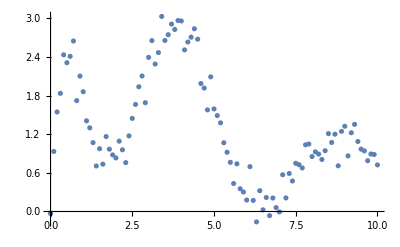

```mathematica
ListPlot[t1]
```

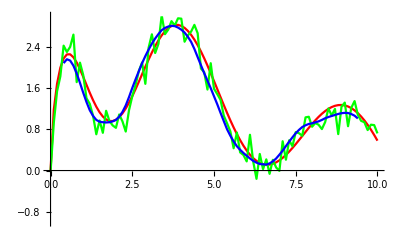

```mathematica
ListLinePlot[{tb,tn,tnp},PlotRange->{{0,10},{-1,3}},PlotStyle->{Red,Green,Blue}]
```

```mathematica
d1=MapThread[{#1,#2}&,{Most[t1⟦;;,1⟧],ListConvolve[{1,-1},t1⟦;;,2⟧]/(1/10)}];
```

```mathematica
d2=MapThread[{#1,#2}&,{Most[tn⟦;;,1⟧],ListConvolve[{1,-1},tn⟦;;,2⟧]/(1/10)}];
```

```mathematica
d2p=MapThread[{#1, #2}&,{d2⟦6;;95,1⟧,ListConvolve[GaussianMatrix[{{5}}],d2⟦;;,2⟧]}];
```

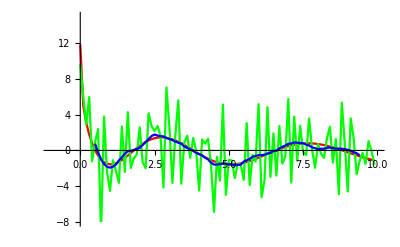

```mathematica
ListLinePlot[{d1,d2,d2p},PlotRange->{{-1,10},{-8,15}},PlotStyle->{Red,Green,Blue}]
```

Т.к. ядро большое, то оно будет упираться в край списка значений, когда будет проходиться по нему и поэтому первые значения не посчитаются. Поэтому для производной и для самих сглаженных значений я брала DataRange от 0.5 до 9.5. Можно заметить, что график производных сглаженных значений близок к графику производных исходных значений

## 5. Свёртка изображений

```mathematica
SetDirectory@NotebookDirectory[];
Import["NG21P10Problem.png"]
ColorConvert[%,"Grayscale"];
Dimensions[X=ImageData[%]]
```

{1024,1024}

```mathematica
Ker={{1,0},{0,1}};
```

```mathematica
ArrayPlot[1-ListConvolve[Ker, GaussianFilter[X,3, Ker]]]
```

```mathematica
ClearAll[kmShow];
kmShow[x_]:=ArrayPlot[x,ColorFunction->GrayLevel]
kmShow[x_,ker_]:=kmShow[ListConvolve[ker,x]]
```

```mathematica
Grid[{kmShow[X,RandomReal[#,{5,5}]]&/@{{-1,1},{0,1}}}]
```

Как видно финальная картинка зависит от типа ядра. Цвета в первом случае размываются. Во втором, остается видна четкая граница

## 6. Фильтрация изображений

```mathematica
Grid[{MatrixPlot[GaussianMatrix[13,#],ColorFunction->"GreenPinkTones",Frame->False,PlotLabel->StringJoin["Order: ",ToString[#]]]&/@{0,{1,0},{{1,0},{0,1}},{{2,0},{0,2}}}},Frame->All]
```

```mathematica
KerG=GaussianMatrix[13,#]&/@{0,{1,0},{{1,0},{0,1}},{{2,0},{0,2}}};
```

```mathematica
Grid[{
kmShow[X,#]&/@KerG}]
```

Первое ядро : цвета остаются, границы не четкие. Второе и третье : делают изображение рельефным (выделяют белый как возвышенность, а черный как впадины). Четвертое : выделяет только границы, рисунок "плоский"

```mathematica
Grid[{kmShow[#[X,15]]&/@{MeanFilter,MedianFilter}}]
```

Усредняющий и медианный фильтры размывают цвета (первый больше, чем другой)